## WHO Latest Data [4]

Possui apenas dados confirmados, sem muita descrição e informação. Creio que não vai dar pra extrair muita coisa, mas deixarei como opção.

```mathematica
latestData = Import["https://raw.githubusercontent.com/globaldothealth/monkeypox/main/latest.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
Normal[Keys[latestData[[1]]]]
```

{_id,Pathogen,ID,Case_status,Pathogen_status,Location_information,Age,Sex_at_birth,Sex_at_birth_other,Gender,Gender_other,Race,Race_other,Ethnicity,Ethnicity_other,Nationality,Nationality_other,Occupation,Healthcare_worker,Previous_infection,Co_infection,Pre_existing_condition,Pregnancy_Status,Vaccination,Vaccine_name,Vaccination_date,Vaccine_side_effects,Symptoms,Date_onset,Date_confirmation,Confirmation_method,Date_of_first_consultation,Hospitalized,Reason_for_hospitalization,Date_hospitalization,Date_discharge_hospital,Intensive_care,Date_admission_ICU,Date_discharge_ICU,Home_monitoring,Isolated,Date_isolation,Outcome,Date_death,Date_recovered,Contact_with_case,Contact_ID,Contact_setting,Contact_setting_other,Contact_animal,Contact_comment,Transmission,Travel_history,Travel_history_entry,Travel_history_start,Travel_history_location,Genomics_Metadata,Accession_Number,Source,Source_II,Source_III,Source_IV,Date_entry,Date_last_modified}

```mathematica
brazilData = Query[Select[ StringContainsQ[ #"Location_information", "Brazil"]&]] @ latestData
```

```mathematica
GroupBy[#Isolated&] @ brazilData
```

Dataset[<>]

## WHO Latest (Deprecated version)

Possui um pouco mais de detalhe nos dados, porém ainda muito disperso. A maioria dos dados são de casos confirmados, porém existem alguns com status “discarded”, só não sei se reflete a realidade baseado nos Boletins publicados no site do Ministério da Saúde.

```mathematica
latestDeprecated = Import["https://raw.githubusercontent.com/globaldothealth/monkeypox/main/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
Normal[Keys[latestDeprecated[[1]]]]
```

{ID,Status,Location,City,Country,Country_ISO3,Age,Gender,Date_onset,Date_confirmation,Symptoms,Hospitalised (Y/N/NA),Date_hospitalisation,Isolated (Y/N/NA),Date_isolation,Outcome,Contact_comment,Contact_ID,Contact_location,Travel_history (Y/N/NA),Travel_history_entry,Travel_history_start,Travel_history_location,Travel_history_country,Genomics_Metadata,Confirmation_method,Source,Source_II,Source_III,Source_IV,Source_V,Source_VI,Source_VII,Date_entry,Date_death,Date_last_modified}

```mathematica
brazilDeprecatedData = Query[Select[ StringContainsQ[ #Country, "Brazil"]&]] @ latestDeprecated
```

Dataset[<>]

```mathematica
GroupBy[#Status&] @ brazilDeprecatedData
```

Dataset[<>]

## WHO Timeseries por país (Deprecated)

Só traz os casos totais e acumulados. Dá pra cruzar com os dados do boletim do site do Ministério da Saúde.

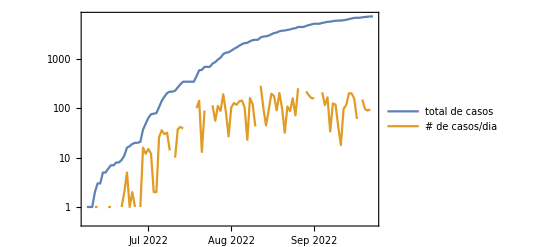

```mathematica
timeseriesData := Import["https://raw.githubusercontent.com/globaldothealth/monkeypox/main/timeseries-country-confirmed-deprecated.csv", "Dataset", "HeaderLines" -> 1];
brazilTimeseries = Query[Select[ StringContainsQ[ #Country, "Brazil"]&]]  @ timeseriesData;
(* Normal[brazilTimeseries[[All, "Date", "Cases"]]] *)
cumulative = TimeSeries[Map[{#Date, #"Cumulative_cases"}&,Normal[brazilTimeseries ]]];
cases = TimeSeries[Map[{#Date, #"Cases"}&,Normal[brazilTimeseries ]]];
DateListLogPlot[{cumulative, cases}, Joined->True, PlotLegends->{"total de casos", "# de casos/dia"}]
```

## OWID [5]

Traz dados consolidados, com um pouco mais de detalhes (casos por dia, total acumulado e mortes). Os dados parecem um pouco mais sanitizados, com a coluna de new_cases_smoothed, que ajuda na geração do gráfico.

```mathematica
owid := Import["https://raw.githubusercontent.com/owid/monkeypox/main/owid-monkeypox-data.csv", "Dataset", "HeaderLines" -> 1];
brazilOwid = Query[Select[ StringContainsQ[ #location, "Brazil"]&]]  @ owid
```

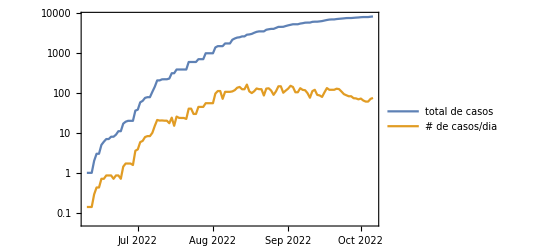

```mathematica
cumulativeTotalCases = TimeSeries[Map[{#date, #"total_cases"}&,Normal[brazilOwid ]]];
newCasesSmoothed = TimeSeries[Map[{#date, #"new_cases_smoothed"}&,Normal[brazilOwid ]]];
DateListLogPlot[{cumulativeTotalCases, newCasesSmoothed}, Joined->True, PlotLegends->{"total de casos", "# de casos/dia"}]
```

## Boletim n. 14 - Ministério da Saúde Brasil

Extraí manualmente a partir da tabela publicada no último boletim do Ministério da Saúde. [3] Os dados estão consolidados por semana epidemiológica, o que é possível cruzar com os dados de outras fontes acima. Tem dados de Suspeitos/Descartados e Exclusões, o que dá pra ser utilizado nas formulas do modelo SEIR.

```mathematica
msbData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Data/monkeypox/boletim-semana-38.csv", "Dataset", "HeaderLines" -> 1]
msbData
```

{Day,/,Month,/,Year}

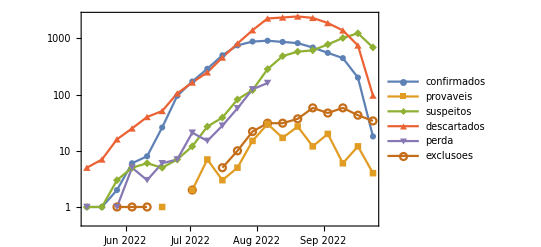

```mathematica
dateFormat = {"Day", "/", "Month", "/", "Year"}
totalConfirmados = TimeSeries[Map[{FromDateString[#Fim, dateFormat], #"Confirmados"}&,Normal[msbData ]]];
totalProvaveis = TimeSeries[Map[{FromDateString[#Fim, dateFormat], #"Prováveis"}&,Normal[msbData ]]];
totalSuspeitos= TimeSeries[Map[{FromDateString[#Fim, dateFormat], #"Suspeitos"}&,Normal[msbData ]]];
totalDescartados= TimeSeries[Map[{FromDateString[#Fim, dateFormat], #"Descartados"}&,Normal[msbData ]]];
totalPerda= TimeSeries[Map[{FromDateString[#Fim, dateFormat], #"Perdas de Seguimento"}&,Normal[msbData ]]];
totalExclusoes= TimeSeries[Map[{FromDateString[#Fim, dateFormat], #"Exclusões"}&,Normal[msbData ]]];
DateListLogPlot[Tooltip[{totalConfirmados, totalProvaveis, totalSuspeitos,totalDescartados, totalPerda, totalExclusoes}], Joined->True, PlotLegends->{"confirmados", "provaveis", "suspeitos", "descartados", "perda", "exclusoes"}, PlotMarkers->{Automatic}]
```

## Dados Literatura

Alguns dados que tirei de alguns artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

### Período de Incubação [1]

```mathematica
incubation = Range[5,21];
avgIncubation = Mean[incubation]
```

13

### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0,3];
rashPhase = Range[7,21];
avgTotalInfection = Mean[Map[Mean] @ {prodomalPhase, rashPhase}];
δ = avgTotalInfection
```

31/4

### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/δ, sendo δ a média do período de infecção total.

## Referências

[1] Monkeypox, a Literature Review: What Is New and Where Does This concerning Virus Come From?

[2] SIR and SIRS models

[3] Monkeypox - Boletim Semana 38

[4] Repositório Monkeypox WHO

[5] Repositório Our Wold In Data